```mathematica
Plot[LaplaceTransform[15764-34199 x+33141 x^2-18826 x^3+6884 x^4-1664 x^5+260 x^6-24 x^7+x^8,x,t],{t,-5,5}, PlotRange->All]
```

NIntegrate::inumri: The integrand ⅇ^(4.9998 x) x has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,5.23043×10^7}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

$Aborted

```mathematica
Log
```

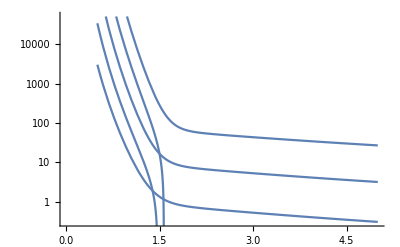

```mathematica
Monitor[Show [Table[LogPlot[LaplaceTransform[ChromaticPolynomial[JacobsThalGraph[k],x],x,t],{t,1/2,5}, PlotRange->{{0,5},{-50000,50000}}],{k,1,5}]],k]
```

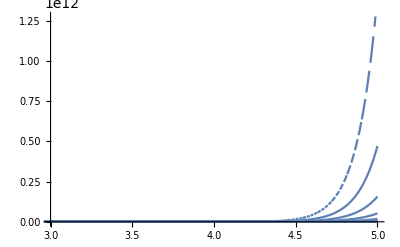

```mathematica
Monitor[Show [Table[Plot[ChromaticPolynomial[JacobsThalGraph[k],x],{x,1/2,5}, PlotRange->{{3,5},All}],{k,1,30}]],k]
```

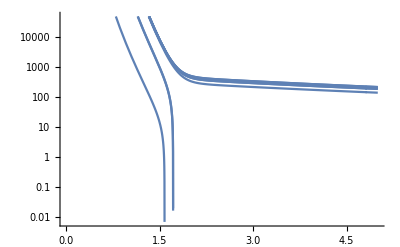

```mathematica
Monitor[Show [Table[LogPlot[LaplaceTransform[ChromaticPolynomial[ReadGrof[k],x],x,t],{t,1/2,5}, PlotRange->{{0,5},{-50000,50000}}],{k,10,1000,100}]],k]
```

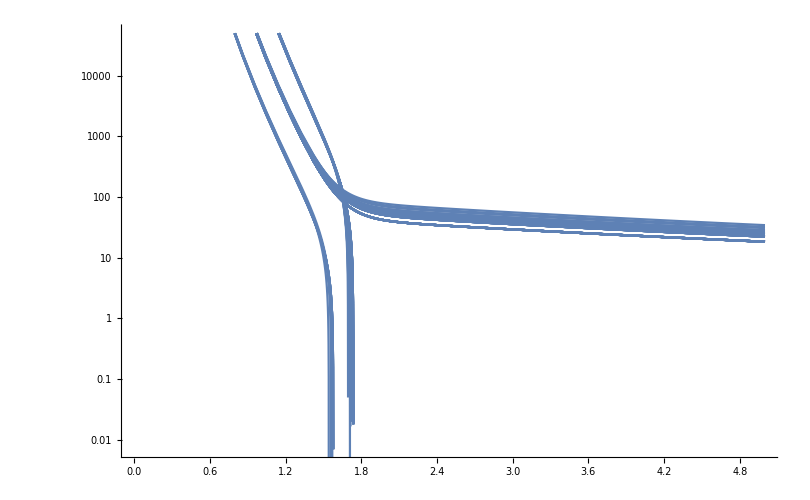

```mathematica
Monitor[Show [Table[LogPlot[LaplaceTransform[ChromaticPolynomial[ReadGrof[k],x],x,t],{t,1/2,5}, PlotRange->{{0,5},{-50000,50000}}],{k,10,100}]],k]
```

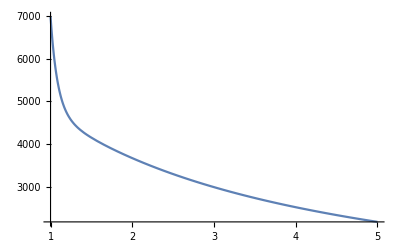

```mathematica
Plot[LaplaceTransform[15764-34199 x+33141 x^2-18826 x^3+6884 x^4-1664 x^5+260 x^6-24 x^7+x^8,x,t],{t,1,5}]
```

```mathematica
FourierTransform[15764-34199 x+33141 x^2-18826 x^3+6884 x^4-1664 x^5+260 x^6-24 x^7+x^8,x,t]
```

15764 √(2 π) DiracDelta[t]+34199 ⅈ √(2 π) DiracDelta'[t]-33141 √(2 π) DiracDelta''[t]-18826 ⅈ √(2 π) DiracDelta^(3)[t]+6884 √(2 π) DiracDelta^(4)[t]+1664 ⅈ √(2 π) DiracDelta^(5)[t]-260 √(2 π) DiracDelta^(6)[t]-24 ⅈ √(2 π) DiracDelta^(7)[t]+√(2 π) DiracDelta^(8)[t]

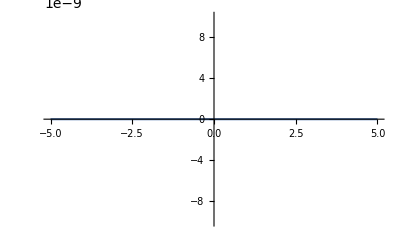

```mathematica
Plot[DiracDelta[t],{t,-5,5}, PlotRange->{All,{-0.00000001,0.00000001}}]
```

```mathematica
Plot[15764 √(2 π) DiracDelta[t]+34199 ⅈ √(2 π) DiracDelta'[t]-33141 √(2 π) DiracDelta''[t]-18826 ⅈ √(2 π) Derivative[3][DiracDelta][t]+6884 √(2 π) Derivative[4][DiracDelta][t]+1664 ⅈ √(2 π) Derivative[5][DiracDelta][t]-260 √(2 π) Derivative[6][DiracDelta][t]-24 ⅈ √(2 π) Derivative[7][DiracDelta][t]+√(2 π) Derivative[8][DiracDelta][t],{t,-5,5}, PlotRange->{All,{-0.00000001,0.00000001}}]
```

-Graphics-

```mathematica
NRoots[FourierTransform[15764-34199 x+33141 x^2-18826 x^3+6884 x^4-1664 x^5+260 x^6-24 x^7+x^8,x,t]==0,t]
```

NRoots::nnumeq: 15764 √(2 π) DiracDelta[t]+34199 ⅈ √(2 π) DiracDelta'[t]-33141 √(2 π) DiracDelta''[t]-18826 ⅈ √(2 π) DiracDelta^(3)[t]+6884 √(2 π) DiracDelta^(4)[t]+1664 ⅈ √(2 π) DiracDelta^(5)[t]-260 √(2 π) DiracDelta^(6)[t]-24 ⅈ √(2 π) DiracDelta^(7)[t]+√(2 π) DiracDelta^(8)[t]==0 is expected to be a polynomial equation in the variable t with numeric coefficients.

NRoots[15764 √(2 π) DiracDelta[t]+34199 ⅈ √(2 π) DiracDelta'[t]-33141 √(2 π) DiracDelta''[t]-18826 ⅈ √(2 π) DiracDelta^(3)[t]+6884 √(2 π) DiracDelta^(4)[t]+1664 ⅈ √(2 π) DiracDelta^(5)[t]-260 √(2 π) DiracDelta^(6)[t]-24 ⅈ √(2 π) DiracDelta^(7)[t]+√(2 π) DiracDelta^(8)[t]==0,t]